## Tarefas

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Partition[{1,2,3,4,5,6,7,8,9,10},2] // TableForm
```

1 | 2
3 | 4
5 | 6
7 | 8
9 | 10

```mathematica
a = RandomInteger[10,{5,5}]
```

(8 | 3 | 2 | 0 | 2
3 | 0 | 1 | 1 | 5
6 | 4 | 5 | 6 | 7
7 | 0 | 9 | 2 | 8
10 | 2 | 9 | 4 | 5)

```mathematica
b = RandomInteger[10,{5,5}]
```

(6 | 3 | 0 | 2 | 5
5 | 7 | 4 | 5 | 0
5 | 5 | 8 | 3 | 2
5 | 2 | 8 | 5 | 6
7 | 10 | 6 | 4 | 2)

```mathematica
aᵀ //TableForm
```

8 | 3 | 6 | 7 | 10
3 | 0 | 4 | 0 | 2
2 | 1 | 5 | 9 | 9
0 | 1 | 6 | 2 | 4
2 | 5 | 7 | 8 | 5

```mathematica
bᵀ // TableForm
```

6 | 5 | 5 | 5 | 7
3 | 7 | 5 | 2 | 10
0 | 4 | 8 | 8 | 6
2 | 5 | 3 | 5 | 4
5 | 0 | 2 | 6 | 2

## Outros:

```mathematica
a.b // TableForm
```

87 | 75 | 40 | 45 | 48
63 | 66 | 46 | 34 | 33
160 | 153 | 146 | 105 | 90
153 | 150 | 136 | 83 | 81
170 | 147 | 142 | 97 | 102

### Vetor de borda

```mathematica
m = ConstantArray[1,{5,5}]
```

{{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}

#### Mascara:

```mathematica
d = ConstantArray[0,{3,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
m[[ 2;;-2]] [[ 2 ;; -2]] = d
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
m // TraditionalForm
```

(1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 1)

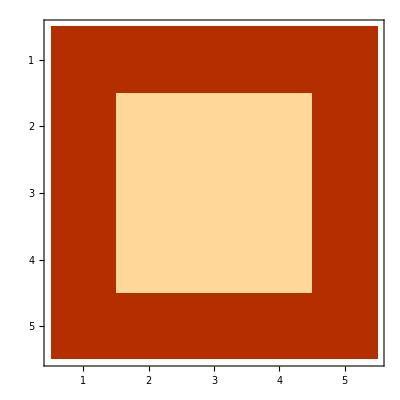

```mathematica
ArrayPlot[{{1,1,1,1,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,1,1,1,1}},PlotTheme->"Web"]
```

### Rnd

```mathematica
mk = RandomInteger[10,{4,4}]; mk //TraditionalForm
```

(8 | 0 | 5 | 4
1 | 4 | 6 | 0
4 | 1 | 6 | 6
6 | 1 | 6 | 4)

```mathematica
Mean[mk]
```

{19/4,3/2,23/4,7/2}

```mathematica
DiagonalMatrix[Range[1,4],-1] // TraditionalForm
```

(0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 4 | 0)

```mathematica
MatrixRank[{{0,0,0,0,0},{1,0,0,0,0},{0,2,0,0,0},{0,0,3,0,0},{0,0,0,4,0}}]
```

4

```mathematica
hi = HistogramList[{1,1,1,2,3,3,4},{1}, "Count"]
```

{{0,1,2,3,4,5},{0,3,1,2,1}}

```mathematica
hii = Delete[hi,{1,-1}] // Transpose
```

{{0,0},{1,3},{2,1},{3,2},{4,1}}

```mathematica
BinCounts[{1,1,1,3,3,4,5,6,7},{1}]
```

{0,3,0,2,1,1,1,1}

```mathematica
Tally[{0,3,0,2,1,1,1,1}]
```

{{0,2},{3,1},{2,1},{1,4}}

```mathematica
SortBy[{{0,2},{3,1},{2,1},{1,4}},Last]
```

```mathematica
{{2,1},{3,1},{0,2},{1,4}} // Last
```

{1,4}